This is the third of three notebooks which accompany the paper “Gravitational Waves on Kerr Black Holes I: Reconstruction of Linearized Metric Perturbations” (https://arxiv.org/abs/2403.20311). This notebook imports the results of Metric Perturbation.nb and shows how to numerically plot a component of a metric perturbation.

```mathematica
<<SpinWeightedSpheroidalHarmonics`

<<Notation`
Symbolize[ParsedBoxWrapper[SubscriptBox["_","_"]]]

(* Set the working directory to this notebook's path to make importing and exporting notebook relative. *)
SetDirectory@NotebookDirectory[];
```

## 1. Setup and Definitions

```mathematica
$Assumptions = {
0 < a < M, 
0 <M+Sqrt[M^2-a^2]< r, 
Element[θ, Reals], 
Element[t, Reals], 
Element[ϕ, Reals],
Element[m,Integers]
};

coord={t,r,θ,ϕ};

Δ=r^2-2M*r+a^2;
Σ=r^2+a^2*Cos[θ]^2;
ζ=r-I*a*Cos[θ];
ζbar=r+I*a*Cos[θ];
ωsub={Conjugate[ω]->ωbar,Conjugate[ωbar]->ω};
K[ω_,m_]:=(r^2+a^2)*ω-a*m;
Kbar[ω_,m_]:=(r^2+a^2)*Conjugate[ω]-a*m;
Q[ω_,m_]:=-a*ω*Sin[θ]+m*Csc[θ];
Qbar[ω_,m_]:=-a*Conjugate[ω]*Sin[θ]+m*Csc[θ];
gBL=-ϵg*{{(1-(2M*r)/Σ),0,0,(a*Sin[θ]^2*(2M*r))/Σ},{0,-Σ/Δ,0,0},{0,0,-Σ,0},{(a*Sin[θ]^2*(2M*r))/Σ,0,0,-(((r^2+a^2)^2-Δ*a^2*Sin[θ]^2)/Σ)*Sin[θ]^2}};
lupBL = {(r^2+a^2)/Δ,1,0,a/Δ};
nupBL = 1/(2*Σ)*{r^2+a^2,-Δ,0,a}; 
mupBL = 1/(Sqrt[2]*ζbar)*{I*a*Sin[θ],0,1,I/Sin[θ]}; 
mbarupBL = 1/(Sqrt[2]*ζ)*{-I*a*Sin[θ],0,1,-I/Sin[θ]};
ldownBL=gBL.lupBL//Simplify;
ndownBL=gBL.nupBL//Simplify;
mdownBL=gBL.mupBL//Simplify;
mbardownBL=gBL.mbarupBL//Simplify;
```

## 2. Radial and Angular Mode Functions

```mathematica
{R2[ω,l,m,r],R2[-ωbar,l,-m,r],Rn2[ω,l,m,r],Rn2[-ωbar,l,-m,r],R2bar[ω,l,m,r],R2bar[-ωbar,l,-m,r],Rn2bar[ω,l,m,r],Rn2bar[-ωbar,l,-m,r]};
Rlist=Flatten[{%,D[%,r],D[%,{r,2}]}];
{S2[ω,l,m,θ],S2[-ωbar,l,-m,θ],Sn2[ω,l,m,θ],Sn2[-ωbar,l,-m,θ],S2bar[ω,l,m,θ],S2bar[-ωbar,l,-m,θ],Sn2bar[ω,l,m,θ],Sn2bar[-ωbar,l,-m,θ]};
Slist=Flatten[{%,D[%,θ],D[%,{θ,2}]}];
```

```mathematica
eqR2=Δ^-s*D[Δ^(s+1)*D[R2[ω,l,m,r],r],r]+((K[ω,m]^2-2*I*s*(r-M)*K[ω,m])/Δ+4*I*s*ω*r-λ2[ω,l,m])*R2[ω,l,m,r]/.s->2;
eqS2=-Sin[θ]^-1*D[Sin[θ]^2*(-Sin[θ]^-1*D[S2[ω,l,m,θ],θ]),θ]+(a^2*ω^2*Cos[θ]^2-(m+s*Cos[θ])^2/Sin[θ]^2-2*a*s*ω*Cos[θ]+s+A)*S2[ω,l,m,θ]/.s->2/.A->λ2[ω,l,m]+2*a*m*ω-a^2*ω^2;
eqRn2=Δ^-s*D[Δ^(s+1)*D[Rn2[ω,l,m,r],r],r]+((K[ω,m]^2-2*I*s*(r-M)*K[ω,m])/Δ+4*I*s*ω*r-λn2[ω,l,m])*Rn2[ω,l,m,r]/.s->-2;
eqSn2=-Sin[θ]^-1*D[Sin[θ]^2*(-Sin[θ]^-1*D[Sn2[ω,l,m,θ],θ]),θ]+(a^2*ω^2*Cos[θ]^2-(m+s*Cos[θ])^2/Sin[θ]^2-2*a*s*ω*Cos[θ]+s+A)*Sn2[ω,l,m,θ]/.s->-2/.A->λn2[ω,l,m]+2*a*m*ω-a^2*ω^2;
eqR2bar=Δ^-s*D[Δ^(s+1)*D[R2bar[ω,l,m,r],r],r]+((Kbar[ω,m]^2+2*I*s*(r-M)*Kbar[ω,m])/Δ-4*I*s*ωbar*r-λ2bar[ω,l,m])*R2bar[ω,l,m,r]/.s->2;
eqS2bar=-Sin[θ]^-1*D[Sin[θ]^2*(-Sin[θ]^-1*D[S2bar[ω,l,m,θ],θ]),θ]+(a^2*ωbar^2*Cos[θ]^2-(m+s*Cos[θ])^2/Sin[θ]^2-2*a*s*ωbar*Cos[θ]+s+A)*S2bar[ω,l,m,θ]/.s->2/.A->λ2bar[ω,l,m]+2*a*m*ωbar-a^2*ωbar^2;
eqRn2bar=Δ^-s*D[Δ^(s+1)*D[Rn2bar[ω,l,m,r],r],r]+((Kbar[ω,m]^2+2*I*s*(r-M)*Kbar[ω,m])/Δ-4*I*s*ωbar*r-λn2bar[ω,l,m])*Rn2bar[ω,l,m,r]/.s->-2;
eqSn2bar=-Sin[θ]^-1*D[Sin[θ]^2*(-Sin[θ]^-1*D[Sn2bar[ω,l,m,θ],θ]),θ]+(a^2*ωbar^2*Cos[θ]^2-(m+s*Cos[θ])^2/Sin[θ]^2-2*a*s*ωbar*Cos[θ]+s+A)*Sn2bar[ω,l,m,θ]/.A->λn2bar[ω,l,m]+2*a*m*ωbar-a^2*ωbar^2/.s->-2;
```

```mathematica
R2sub=D[R2[ω0_,l0_,m0_,r],{r,2}]:>Evaluate[Simplify[Solve[eqR2==0,D[R2[ω,l,m,r],{r,2}]][[1]][[1]][[2]]]]/.ω->ω0/.ωbar->Conjugate[ω0]/.l->l0/.m->m0;
Rn2sub=D[Rn2[ω0_,l0_,m0_,r],{r,2}]:>Evaluate[Simplify[Solve[eqRn2==0,D[Rn2[ω,l,m,r],{r,2}]][[1]][[1]][[2]]]]/.ω->ω0/.ωbar->Conjugate[ω0]/.l->l0/.m->m0;
R2barsub=D[R2bar[ω0_,l0_,m0_,r],{r,2}]:>Evaluate[Simplify[Solve[eqR2bar==0,D[R2bar[ω,l,m,r],{r,2}]][[1]][[1]][[2]]]]/.ω->ω0/.ωbar->Conjugate[ω0]/.l->l0/.m->m0;
Rn2barsub=D[Rn2bar[ω0_,l0_,m0_,r],{r,2}]:>Evaluate[Simplify[Solve[eqRn2bar==0,D[Rn2bar[ω,l,m,r],{r,2}]][[1]][[1]][[2]]]]/.ω->ω0/.ωbar->Conjugate[ω0]/.l->l0/.m->m0;
Rsub=Flatten[{R2sub,Rn2sub,R2barsub,Rn2barsub}];
```

```mathematica
S2sub=D[S2[ω0_,l0_,m0_,θ],{θ,2}]:>Evaluate[Simplify[Solve[eqS2==0,D[S2[ω,l,m,θ],{θ,2}]][[1]][[1]][[2]]]]/.ω->ω0/.ωbar->Conjugate[ω0]/.l->l0/.m->m0;
Sn2sub=D[Sn2[ω0_,l0_,m0_,θ],{θ,2}]:>Evaluate[Simplify[Solve[eqSn2==0,D[Sn2[ω,l,m,θ],{θ,2}]][[1]][[1]][[2]]]]/.ω->ω0/.ωbar->Conjugate[ω0]/.l->l0/.m->m0;
S2barsub=D[S2bar[ω0_,l0_,m0_,θ],{θ,2}]:>Evaluate[Simplify[Solve[eqS2bar==0,D[S2bar[ω,l,m,θ],{θ,2}]][[1]][[1]][[2]]]]/.ω->ω0/.ωbar->Conjugate[ω0]/.l->l0/.m->m0;
Sn2barsub=D[Sn2bar[ω0_,l0_,m0_,θ],{θ,2}]:>Evaluate[Simplify[Solve[eqSn2bar==0,D[Sn2bar[ω,l,m,θ],{θ,2}]][[1]][[1]][[2]]]]/.ω->ω0/.ωbar->Conjugate[ω0]/.l->l0/.m->m0;
Ssub=Flatten[{S2sub,Sn2sub,S2barsub,Sn2barsub}];
```

```mathematica
{eqR2,eqRn2,eqR2bar,eqRn2bar}/.Rsub/.ωsub//Simplify
{eqS2,eqSn2,eqS2bar,eqSn2bar}/.Ssub/.ωsub//Simplify
```

{0,0,0,0}

{0,0,0,0}

## 3. Radial and Angular Modes in Terms of Heun Functions

```mathematica
(* Subscripted definitions have to be done outside of the initialization blocks. *)
SubPlus[r]=M+√(M^2-a^2);
SubMinus[r]=M-√(M^2-a^2);
SubPlus[c]=(2 M SubPlus[r])/(SubPlus[r]-SubMinus[r]);
SubMinus[c]=(2 M SubMinus[r])/(SubPlus[r]-SubMinus[r]);
SubPlus[Ω]=a/(2 M SubPlus[r]);
SubMinus[Ω]=a/(2 M SubMinus[r]);
```

### Angular Modes

```mathematica
(* Explicit solutions to the TAE in terms of confluent Heun functions. *)
Shat2[s_,ω_,l_,m_,θ_]:=Module[{μ1,μ2,β,p},
μ1=Abs[s+m]/2;
μ2=Abs[s-m]/2;
β=2*a*ω*(μ1+μ2+s+1);
p=-λ2[ω,l,m]-2*m*a*ω+2*a*ω*(μ1-μ2)+(μ1+μ2)^2+μ1+μ2-s*(s+1);
(1-Cos[θ])^μ1(1+Cos[θ])^μ2 Exp[a*ω*Cos[θ]]HeunC[-p+β,2*β,2*μ2+1,2*μ1+1,4*a*ω,(1+Cos[θ])/2]
];
Shatn2[s_,ω_,l_,m_,θ_]:=Module[{μ1,μ2,β,p},
μ1=Abs[s+m]/2;
μ2=Abs[s-m]/2;
β=2*a*ω*(μ1+μ2+s+1);
p=-λn2[ω,l,m]-2*m*a*ω+2*a*ω*(μ1-μ2)+(μ1+μ2)^2+μ1+μ2-s*(s+1);
(1-Cos[θ])^μ1(1+Cos[θ])^μ2 Exp[a*ω*Cos[θ]]HeunC[-p+β,2*β,2*μ2+1,2*μ1+1,4*a*ω,(1+Cos[θ])/2]
];

(* The solutions are solutions *)
eqS2==0/.{S2->Function[{ω,l,m,θ},Shat2[2,ω,l,m,θ]]} //FullSimplify
eqSn2==0/.{Sn2->Function[{ω,l,m,θ},Shatn2[-2,ω,l,m,θ]]} //FullSimplify
```

True

True

### Radial Modes

```mathematica
(* Explicit solutions to the TRE in terms of confluent Heun functions. *)
Rhat2in[s_,ω_,l_,m_,r_]:=Module[{ξ1,ξ2,γ,δ,ϵ,α,q},
γ=2ξ1+s+1;
δ=2ξ2+s+1;
ϵ=-2 ⅈ ω(SubPlus[r]-SubMinus[r]);
α=-2 ⅈ ω(2s+1)(SubPlus[r]-SubMinus[r]);
q=-2ⅈ ω SubPlus[r](2s+1)+λ2[ω,l,m];
ξ1=ⅈ SubPlus[c](ω-m SubPlus[Ω]);
ξ2=-ⅈ SubMinus[c](ω-m SubMinus[Ω]);
(SubPlus[r]-SubMinus[r])^(-ξ2-s)(r-SubPlus[r])^(-ξ1-s)(r-SubMinus[r])^ξ2 Exp[ⅈ ω (r-SubPlus[r])]HeunC[q+(ϵ-δ)(1-γ),α+ϵ(1-γ),2-γ,δ,ϵ,-(r-SubPlus[r])/(SubPlus[r]-SubMinus[r])]
];
Rhat2out[s_,ω_,l_,m_,r_]:=Module[{ξ1,ξ2,γ,δ,ϵ,α,q},
γ=2ξ1+s+1;
δ=2ξ2+s+1;
ϵ=-2 ⅈ ω(SubPlus[r]-SubMinus[r]);
α=-2 ⅈ ω(2s+1)(SubPlus[r]-SubMinus[r]);
q=-2ⅈ ω SubPlus[r](2s+1)+λ2[ω,l,m];
ξ1=ⅈ SubPlus[c](ω-m SubPlus[Ω]);
ξ2=-ⅈ SubMinus[c](ω-m SubMinus[Ω]);
(SubPlus[r]-SubMinus[r])^-ξ2(r-SubPlus[r])^ξ1(r-SubMinus[r])^ξ2 Exp[ⅈ ω(r-SubPlus[r])]HeunC[q,α,γ,δ,ϵ,-(r-SubPlus[r])/(SubPlus[r]-SubMinus[r])]
];
Rhatn2in[s_,ω_,l_,m_,r_]:=Module[{ξ1,ξ2,γ,δ,ϵ,α,q},
γ=2ξ1+s+1;
δ=2ξ2+s+1;
ϵ=-2 ⅈ ω(SubPlus[r]-SubMinus[r]);
α=-2 ⅈ ω(2s+1)(SubPlus[r]-SubMinus[r]);
q=-2ⅈ ω SubPlus[r](2s+1)+λn2[ω,l,m];
ξ1=ⅈ SubPlus[c](ω-m SubPlus[Ω]);
ξ2=-ⅈ SubMinus[c](ω-m SubMinus[Ω]);
(SubPlus[r]-SubMinus[r])^(-ξ2-s)(r-SubPlus[r])^(-ξ1-s)(r-SubMinus[r])^ξ2 Exp[ⅈ ω (r-SubPlus[r])]HeunC[q+(ϵ-δ)(1-γ),α+ϵ(1-γ),2-γ,δ,ϵ,-(r-SubPlus[r])/(SubPlus[r]-SubMinus[r])]
];
Rhatn2out[s_,ω_,l_,m_,r_]:=Module[{ξ1,ξ2,γ,δ,ϵ,α,q},
γ=2ξ1+s+1;
δ=2ξ2+s+1;
ϵ=-2 ⅈ ω(SubPlus[r]-SubMinus[r]);
α=-2 ⅈ ω(2s+1)(SubPlus[r]-SubMinus[r]);
q=-2ⅈ ω SubPlus[r](2s+1)+λn2[ω,l,m];
ξ1=ⅈ SubPlus[c](ω-m SubPlus[Ω]);
ξ2=-ⅈ SubMinus[c](ω-m SubMinus[Ω]);
(SubPlus[r]-SubMinus[r])^-ξ2(r-SubPlus[r])^ξ1(r-SubMinus[r])^ξ2 Exp[ⅈ ω(r-SubPlus[r])]HeunC[q,α,γ,δ,ϵ,-(r-SubPlus[r])/(SubPlus[r]-SubMinus[r])]
];

(* The solutions are solutions *)
eqR2==0/.{R2->Function[{ω,l,m,r},Rhat2in[2,ω,l,m,r]]} //FullSimplify
eqR2==0/.{R2->Function[{ω,l,m,r},Rhat2out[2,ω,l,m,r]]} //FullSimplify
eqRn2==0/.{Rn2->Function[{ω,l,m,r},Rhatn2in[-2,ω,l,m,r]]} //FullSimplify
eqRn2==0/.{Rn2->Function[{ω,l,m,r},Rhatn2out[-2,ω,l,m,r]]} //FullSimplify
```

True

True

True

«1 more identical outputs»

```mathematica
<<"./metric-perturbations/habIRG.mx"
```

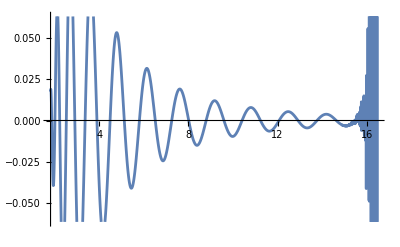

```mathematica
(* Symbolic conjugation *)
conjugate[exp_]:=Module[{},exp/.Complex[a_,b_]:> Complex[a,-b]]
complexSub={A->Subscript[A, x]+ⅈ Subscript[A, y],Abar->Subscript[A, x]-ⅈ Subscript[A, y],B->Subscript[B, x]+ⅈ Subscript[B, y],Bbar->Subscript[B, x]-ⅈ Subscript[B, y],ω->Subscript[ω, x]+ⅈ Subscript[ω, y],ωbar->Subscript[ω, x]-ⅈ Subscript[ω, y]};
modeSub ={
S2->Function[{ω,l,m,θ},Shat2[2,ω,l,m,θ]],
Sn2->Function[{ω,l,m,θ},Shatn2[-2,ω,l,m,θ]],
S2bar->Function[{ω,l,m,θ},conjugate[Shat2[2,ω,l,m,θ]]],
Sn2bar->Function[{ω,l,m,θ},conjugate[Shatn2[-2,ω,l,m,θ]]],
R2->Function[{ω,l,m,r},Rhat2in[2,ω,l,m,r]],
Rn2->Function[{ω,l,m,r},Rhatn2in[-2,ω,l,m,r]],
R2bar->Function[{ω,l,m,r},conjugate[Rhat2in[2,ω,l,m,r]]],
Rn2bar->Function[{ω,l,m,r},conjugate[Rhatn2in[-2,ω,l,m,r]]]
};

rplus[a_,M_]:=M+√(M^2-a^2)

SubStar[a]=0.43;
SubStar[M]=0.88;
SubStar[m]=2;
SubStar[l]=3;
Subscript[ω, xstar]=3.2;
Subscript[ω, ystar]=0;

(* The nn tetrad component in IRG. *)
habIRG[[2,2]]/.complexSub;
%/.modeSub;

(* Substitute numerical values of the separation constants. *)
%/.{λ2->Function[{ω,l,m},SpinWeightedSpheroidalEigenvalue[2,l,m,SubStar[a] ω]],λn2->Function[{ω,l,m},SpinWeightedSpheroidalEigenvalue[-2,l,m,SubStar[a] ω]]};

(* Substitute on the remaining parameters. *)
%/.{Subscript[A, x]->1,Subscript[A, y]->0,Subscript[B, x]->0,Subscript[B, y]->0,M->SubStar[M],a->SubStar[a],m->SubStar[m],ϵg->1,l->SubStar[l],Subscript[ω, x]->Subscript[ω, xstar],Subscript[ω, y]->Subscript[ω, ystar],ϕ->0.5,t->1.2,θ->Pi/4};

(* Plot the result. *)
Plot[%//Chop,{r,1.1rplus[SubStar[a],SubStar[M]],10 rplus[SubStar[a],SubStar[M]]}]
```